Non-Unitary Dynamics of Quantum States

How Statistical Mixture Arisespaclet:QuantumMob/QuantumPlaybook/tutorial/NonUnitaryDynamicsOfQuantumStates#148953960 | Kraus Operatorspaclet:QuantumMob/QuantumPlaybook/tutorial/NonUnitaryDynamicsOfQuantumStates#2005977689

Here, we gives a illustration how non-unitary dynamics of quantum states arise from the interaction of the system with its environment.

Supermappaclet:QuantumMob/Q3/ref/SupermapQuantumMob Package Symbol | Mapping of operators to other operators
PartialTracepaclet:QuantumMob/Q3/ref/PartialTraceQuantumMob Package Symbol | Partial trace over a subsystem of the system
LindbladSolvepaclet:QuantumMob/Q3/ref/LindbladSolveQuantumMob Package Symbol | Solution of the Lindblad equation (also known as quantum master equation)

Functions related to non-unitary dynamics of quantum states.

Make sure that the Q3 package is loaded to use the demonstrations in this documentation.

```mathematica
Needs["QuantumMob`Q3`"]
```

Throughout this document, symbol S will be used to denote qubits and Pauli operators on them.

```mathematica
Let[Qubit,S]
```

How Statistical Mixture Arises

Let us consider a total system consisting of two qubits, one representing the “system” and the other the “environment”:

```mathematica
SS=S[{1,2},$]
```

{S_(,,1),S_(,,2)}

Initially, the total system is assumed to be in a product state.

```mathematica
in=Ket[SS]
```

0_(,,S_(,,1))0_(,,S_(,,2))

Suppose that we want to perform a single-qubit rotation around the x-axis. The required Hamiltonian of the system involves the Pauli-X operator:

```mathematica
H0=S[1,1]*Ω/2;
H0//PauliForm
```

X/2

We choose Ω as our basic energy scale to measure all other energies  and time:

```mathematica
Ω=1
```

1

The system is coupled to the environment via the Ising-type YY interaction. Here, J is the coupling constant:

```mathematica
Hint=J/2*S[1,2]**S[2,2];
Hint//PauliForm
Let[Real,J]
```

(J Y⊗Y)/2

Set the total Hamiltonian of the total system:

```mathematica
HH=H0+Hint;
HH//PauliForm
```

(X⊗I)/2+(J Y⊗Y)/2

The evolution of the total system as a closed system is governed by this time-evolution operator:

```mathematica
U[t_]=MultiplyExp[-I*t*HH]//Elaborate;
U[t]//PauliForm
Let[Real,t]
```

1/2 ⅇ^(-1/2 ⅈ √(1+J^2) t) (1+ⅇ^(ⅈ √(1+J^2) t)) I⊗I-(ⅇ^(-1/2 ⅈ √(1+J^2) t) (-1+ⅇ^(ⅈ √(1+J^2) t)) X⊗I)/(2 √(1+J^2))-(ⅇ^(-1/2 ⅈ √(1+J^2) t) (-1+ⅇ^(ⅈ √(1+J^2) t)) J Y⊗Y)/(2 √(1+J^2))

The above expression looks simpler with the trigonometric functions than the exponential function:

```mathematica
U[t_]=MultiplyExp[-I*t*HH]//Elaborate//ExpToTrig;
U[t]//PauliForm
```

1/2 I⊗I (Cos[1/2 √(1+J^2) t]-ⅈ Sin[1/2 √(1+J^2) t]) (1+Cos[√(1+J^2) t]+ⅈ Sin[√(1+J^2) t])-(X⊗I (Cos[1/2 √(1+J^2) t]-ⅈ Sin[1/2 √(1+J^2) t]) (-1+Cos[√(1+J^2) t]+ⅈ Sin[√(1+J^2) t]))/(2 √(1+J^2))-(J Y⊗Y (Cos[1/2 √(1+J^2) t]-ⅈ Sin[1/2 √(1+J^2) t]) (-1+Cos[√(1+J^2) t]+ⅈ Sin[√(1+J^2) t]))/(2 √(1+J^2))

Get the final state of the total system:

```mathematica
out=U[t]**in
```

Cos[1/2 √(1+J^2) t] 0_(,,S_(,,1))0_(,,S_(,,2))-(ⅈ 1_(,,S_(,,1))0_(,,S_(,,2)) Sin[1/2 √(1+J^2) t])/(√(1+J^2))+(ⅈ J 1_(,,S_(,,1))1_(,,S_(,,2)) Sin[1/2 √(1+J^2) t])/(√(1+J^2))

Note that the above state has entanglement between the system and environment. To see this, the environment is traced out. After all, we have no access to the environment.

```mathematica
rho=PartialTrace[out,SS,S[2]]//Elaborate
Matrix[rho,S[1]]//MatrixForm
```

1/2+(ⅈ ⅇ^(-ⅈ √(1+J^2) t) (-1+ⅇ^(2 ⅈ √(1+J^2) t)) S_(,,1)^(,,Y))/(4 √(1+J^2))+1/4 ⅇ^(-ⅈ √(1+J^2) t) (1+ⅇ^(2 ⅈ √(1+J^2) t)) S_(,,1)^(,,Z)

(1/2+1/4 ⅇ^(-ⅈ √(1+J^2) t)+1/4 ⅇ^(ⅈ √(1+J^2) t) | -(ⅇ^(-ⅈ √(1+J^2) t))/(4 √(1+J^2))+(ⅇ^(ⅈ √(1+J^2) t))/(4 √(1+J^2))
(ⅇ^(-ⅈ √(1+J^2) t))/(4 √(1+J^2))-(ⅇ^(ⅈ √(1+J^2) t))/(4 √(1+J^2)) | 1/2-1/4 ⅇ^(-ⅈ √(1+J^2) t)-1/4 ⅇ^(ⅈ √(1+J^2) t))

The degree of entanglement between the system and environment in state out can be quantified by the von Neumann entanglement of reduced density operator rho.

```mathematica
entropy[t_]=VonNeumannEntropy[PartialTrace[out,S[2]]]
```

-1/(4 √(1+J^2) Log[2])ⅇ^(-ⅈ √(1+J^2) t) (2 ⅇ^(ⅈ √(1+J^2) t) √(1+J^2)-√(4 ⅇ^(2 ⅈ √(1+J^2) t)+J^2+2 ⅇ^(2 ⅈ √(1+J^2) t) J^2+ⅇ^(4 ⅈ √(1+J^2) t) J^2)) Log[(ⅇ^(-ⅈ √(1+J^2) t) (2 ⅇ^(ⅈ √(1+J^2) t) √(1+J^2)-√(4 ⅇ^(2 ⅈ √(1+J^2) t)+J^2+2 ⅇ^(2 ⅈ √(1+J^2) t) J^2+ⅇ^(4 ⅈ √(1+J^2) t) J^2)))/(4 √(1+J^2))]-1/(4 √(1+J^2) Log[2])ⅇ^(-ⅈ √(1+J^2) t) (2 ⅇ^(ⅈ √(1+J^2) t) √(1+J^2)+√(4 ⅇ^(2 ⅈ √(1+J^2) t)+J^2+2 ⅇ^(2 ⅈ √(1+J^2) t) J^2+ⅇ^(4 ⅈ √(1+J^2) t) J^2)) Log[(ⅇ^(-ⅈ √(1+J^2) t) (2 ⅇ^(ⅈ √(1+J^2) t) √(1+J^2)+√(4 ⅇ^(2 ⅈ √(1+J^2) t)+J^2+2 ⅇ^(2 ⅈ √(1+J^2) t) J^2+ⅇ^(4 ⅈ √(1+J^2) t) J^2)))/(4 √(1+J^2))]

Plot the entropy as a function of time:

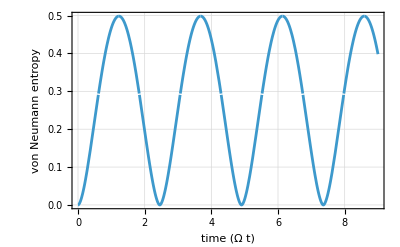

```mathematica
Block[
{J=0.8},
Plot[Chop@entropy[t],{t,0,9},
PlotRange->All,
FrameLabel->{"time (Ω t)","von Neumann entropy"}]
]
```

Kraus Operators

```mathematica
Let[Complex,c]
```

Let {ε_0,ε_1} be an orthonormal basis of the “environment”. Then, starting from the unitary interaction and the initial state of the environment, one can construct two Kraus operators as follows.

-Graphics-

-Graphics-

For the particular example given in the precious section, we first construct dyadic products acting on the “environment”:

```mathematica
d0=Dyad[Ket[S[2]->0],Ket[S[2]->0],S@{2}]
d1=Dyad[Ket[S[2]->0],Ket[S[2]->1],S@{2}]
```

0_(,,S_(,,2))0_(,,S_(,,2))

0_(,,S_(,,2))1_(,,S_(,,2))

Now, construct the Kraus elements by tracing out the environment:

```mathematica
krs0=PartialTrace[U[t]**d0,S[2]]//Elaborate
krs1=PartialTrace[U[t]**d1,S[2]]//Elaborate
```

1/2 ⅇ^(-1/2 ⅈ √(1+J^2) t) (1+ⅇ^(ⅈ √(1+J^2) t))-(ⅇ^(-1/2 ⅈ √(1+J^2) t) (-1+ⅇ^(ⅈ √(1+J^2) t)) S_(,,1)^(,,X))/(2 √(1+J^2))

-(ⅈ ⅇ^(-1/2 ⅈ √(1+J^2) t) (-1+ⅇ^(ⅈ √(1+J^2) t)) J S_(,,1)^(,,Y))/(2 √(1+J^2))

Check if the resulting Kraus elements satisfy the trace-preserving condition:

```mathematica
Dagger[krs0]**krs0+Dagger[krs1]**krs1//Simplify
```

1

Finally, obtain the density operator using these Kraus elements and compare it with rho that was obtained by tracing out the environment in the composite state out:

```mathematica
new=Supermap[{krs0,krs1}][Dyad[in,in,S@{1}]]//Elaborate//ExpToTrig//Garner
```

1/2+1/2 Cos[√(1+J^2) t] S_(,,1)^(,,Z)-(S_(,,1)^(,,Y) Sin[√(1+J^2) t])/(2 √(1+J^2))

| Related Guides
▪Quantum Computation and Information

| Related Tech Notes
▪A Quantum Playbook
▪Quantum States
▪Quantum Noise and Decoherence

| Related Links
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer, 2022).